```mathematica
SetDirectory[NotebookDirectory[]];
```

## using FixedPoint

```mathematica
Clear["Global`*"]
```

```mathematica
getFixedPoint[f_,x0_, rIn_]:=
FixedPoint[f/.{r->rIn},x0, maxIterations]

fixedPointVsR[f_,x0_]:= Table[
{r,getFixedPoint[f,x0,r]},
{r,rRange[[1]],rRange[[2]],rStep}
]

bifurcationDiagram[map_]:=Module[{f = map },

Print["calculating points..."];
fixedPointsVsR=Table[
fixedPointVsR[f,x0],
{x0,x0Range[[1]],x0Range[[2]],x0Step}
];

Print["plotting points..."];
ListPlot[
fixedPointsVsR,
PlotStyle -> Directive[
PointSize[.001],
Black
],
PlotRange->Automatic,
Axes -> False;
Frame -> True;
ImageSize->Large
]
]
```

```mathematica
logisticMap[x_]:= r x (1-x)
cubicMap[x_]:=r x^3+ (1 - r) x
gaussMap[x_]:= Exp[- 4.9 x^2] + r
```

```mathematica
rStep = .01;rRange = {3, 4};
x0Step = .01;x0Range = {0,1};

maxIterations = 500;
```

calculating points...

plotting points...

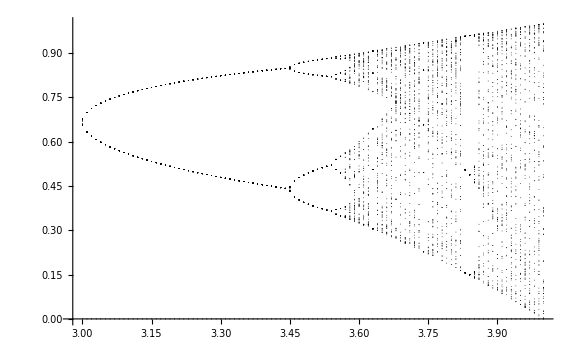

```mathematica
bifurcationDiagram[logisticMap]
```

## using While loop

```mathematica
Clear["Global`*"]
```

```mathematica
maxItHits = 0; minResHits = 0;
```

```mathematica
getFixedPoint[f_,x0_, r_]:=
Module[{x = x0, i = 0},
While[Abs[x - f[x,r]] > minResidual,
x = f[x,r];
If[i > maxIterations,
maxItHits++;
Break[];
];
i++;
];
If[i ≤ maxIterations,
minResHits++;
];
x
]

fixedPointVsR[f_,x0_]:= Table[
{r,getFixedPoint[f,x0,r]},
{r,rRange[[1]],rRange[[2]],rStep}
]

bifurcationDiagram[map_]:=Module[{f = map },

Print["calculating points..."];
fixedPointsVsR=Table[
fixedPointVsR[f,x0],
{x0,x0Range[[1]],x0Range[[2]],x0Step}
];
Print["maxItHits: ", maxItHits, ", minResHits: ", minResHits];

Print["plotting points..."];
ListPlot[
fixedPointsVsR,
PlotStyle -> Directive[PointSize[0],Black],
PlotRange->Automatic,
Axes -> False;
Frame -> True;
ImageSize->Large
]
]
```

```mathematica
logisticMap[x_,r_]:= r x (1-x)
cubicMap[x_,r_]:=r x^3+ (1 - r) x
gaussMap[x_,r_]:= Exp[- 4.9 x^2] + r
```

```mathematica
rStep = .01;rRange = {3,4};
x0Step = .01;x0Range = {0,1};

minResidual = 1*10^-3;
maxIterations = 500;
```

calculating points...

maxItHits: 9389, minResHits: 812

plotting points...

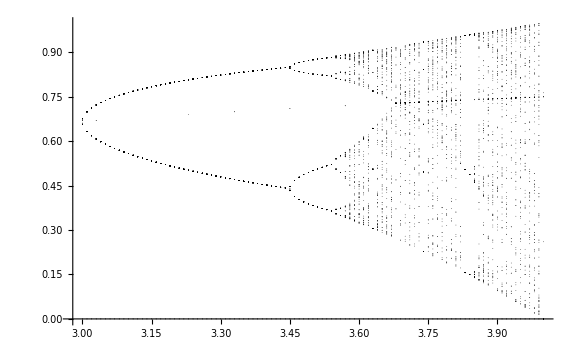

```mathematica
bifurcationDiagram[logisticMap]
```

## color fun

```mathematica
Clear["Global`*"]
```

```mathematica
maxIterates = 20;
resolution = .005;
rMin = 3.2; rMax = 3.65;
```

```mathematica
fixedPointAtR[f_,x0In_,rIn_]:=Module[
{x0 = x0In},
fAtR[x_]= f[x]/.{r -> rIn};
FixedPoint[fAtR,x0,maxIterates]
]
```

```mathematica
fixedPointVsR[f_,x0In_]:= Table[
{r,fixedPointAtR[f,x0In, r]},
{r,rMin,rMax,resolution}
]
```

```mathematica
bifurcationDiagram[map_]:=Module[{f = map },
fixedPointsVsR= Union[ (* union gives a list containing seperate lists for each i=x0 *)
Table[
fixedPointVsR[f,x0],
{x0,.005,1,.008}
]
];
ListPlot[fixedPointsVsR,
 Joined -> True,
InterpolationOrder->3,(* smoothness *)
PlotStyle -> Thickness[.002],
PlotTheme->"SapphireColor",
PlotRange->Automatic,
AspectRatio->1,
ImageSize->600
]
]
```

```mathematica
logisticMap[x_]:= r x (1-x)
```

```mathematica
bifurcationDiagram[logisticMap]
```

-Graphics-